# Homework 6

## STA 445 Probability and Statistics I

Fall 2022

Peter Cullen Burbery

Marshall University statistics and mathematics department

Thursday 8 December 2022

## 4.16

```mathematica
f=y↦Piecewise[{{1/2(2-y), 0<=y<=2}, {0, !(0<=y<=2)}}]
```

Function[y,Piecewise[{{(2-y)/2, 0≤y≤2}, {0, !0≤y≤2}}]]

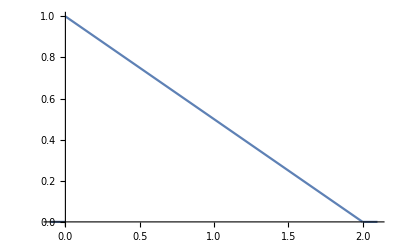

```mathematica
Plot[f[y],{y,-1/10,2+1/10}]
```

```mathematica
F=y↦Piecewise[{{y-y^2/4, 0<=y<=2}, {0, !(0<=y<=2)}}]
```

Function[y,Piecewise[{{y-y^2/4, 0≤y≤2}, {0, !0≤y≤2}}]]

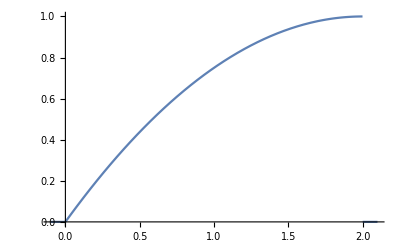

```mathematica
Plot[F[y],{y,-1/10,2+1/10}]
```

```mathematica
F[2]-F[1]
```

1/4

```mathematica
f[2]
```

0

```mathematica
f[1]
```

1/2

```mathematica
∫_(-∞)^∞ ⅇ^(t x)f[x]ⅆx
```

(-1+ⅇ^(2 t)-2 t)/(2 t^2)

```mathematica
∫_(-∞)^∞ ⅇ^(t x)f[x]ⅆx//TraditionalForm
```

(-2 t+ⅇ^(2 t)-1)/(2 t^2)

```mathematica
m=t↦∫_(-∞)^∞ ⅇ^(t x)f[x]ⅆx
```

Function[t,∫_(-∞)^∞ ⅇ^(t x) f[x]ⅆx]

```mathematica
m'[0]
```

2/3

```mathematica
m[t]
```

(-1+ⅇ^(2 t)-2 t)/(2 t^2)

```mathematica
m'[t]
```

(1-ⅇ^(2 t)+t+ⅇ^(2 t) t)/t^3

```mathematica
m''[t]
```

(-3+3 ⅇ^(2 t)-2 t-4 ⅇ^(2 t) t+2 ⅇ^(2 t) t^2)/t^4

```mathematica
m''[0]
```

2/3

```mathematica
m''[0]-m'[0]
```

0

```mathematica
m''[0]-m'[0]^2
```

2/9

## 4.51

```mathematica
cycleTimeDistribution=QuantityDistribution[UniformDistribution[{50,70}],"Minutes"]
```

QuantityDistribution[UniformDistribution[{50,70}], min]

```mathematica
Probability[c>Quantity[65, "Minutes"]\[Conditioned]c>Quantity[55, "Minutes"],c\[Distributed]cycleTimeDistribution]
```

1/3

## 4.52

### mean

```mathematica
Mean[cycleTimeDistribution]
```

60 min

```mathematica
Expectation[c,c\[Distributed]cycleTimeDistribution]
```

60 min

### variance

```mathematica
Variance[cycleTimeDistribution]
Variance[cycleTimeDistribution]//N
```

100/3 min^2

33.3333 min^2

```mathematica
Expectation[(c-Mean[cycleTimeDistribution])^2,c\[Distributed]cycleTimeDistribution]
Expectation[(c-Mean[cycleTimeDistribution])^2,c\[Distributed]cycleTimeDistribution]//N
```

100/3 min^2

33.3333 min^2

## 4.73

```mathematica
widthOfBoltsOfFabricDistribution=QuantityDistribution[NormalDistribution[950,10],"Millimeters"]
```

QuantityDistribution[NormalDistribution[950,10], mm]

### a

```mathematica
Probability[Quantity[947, "Millimeters"]<=p<=Quantity[958, "Millimeters"],p\[Distributed]widthOfBoltsOfFabricDistribution]
```

1/2 (Erf[3/(10 √2)]+Erf[(2 √2)/5])

```mathematica
NProbability[Quantity[947, "Millimeters"]<=p<=Quantity[958, "Millimeters"],p\[Distributed]widthOfBoltsOfFabricDistribution,WorkingPrecision->400]
```

0.4060560236055559517309971913499218279633868735178010394564937353215478260301655220049803018068516432332928316137740720409256094486854599825497182371365002991273989120292766451960469474337274959768354183939507710598311881453974550969904726925768965606310273435023002100114601273098692009238072944551348652718247037033560310875010747449924691819644021686653737976636574248659970192154445006876323254397

### b

```mathematica
InverseCDF[widthOfBoltsOfFabricDistribution,0.8531]
```

960.498 mm

```mathematica
InverseCDF[widthOfBoltsOfFabricDistribution,0.8531]//FullForm
```

Quantity[960.498,"Millimeters"]

## 4.88

```mathematica
earthquakeMagnitudes=ExponentialDistribution[2.4]
```

ExponentialDistribution[2.4]

### a

```mathematica
Probability[m>3.0,m\[Distributed]earthquakeMagnitudes]
```

0.000746586

### b

```mathematica
Probability[2.0<m<3.0,m\[Distributed]earthquakeMagnitudes]
```

0.00748316

## 4.90

```mathematica
Probability[m>5.0,m\[Distributed]earthquakeMagnitudes]
```

6.14421×10^-6

```mathematica
Probability[c>=1,c\[Distributed]BinomialDistribution[10,Probability[m>5.0,m\[Distributed]earthquakeMagnitudes]]]
```

0.0000614404

## 4.94

### a

```mathematica
carbonMonoxide=QuantityDistribution[ExponentialDistribution[3.6],"PartsPerMillion"]
```

QuantityDistribution[ExponentialDistribution[3.6], ppm]

```mathematica
Probability[p>Quantity[9, "PartsPerMillion"],p\[Distributed]carbonMonoxide]
```

8.48904×10^-15

### b

```mathematica
newCarbonMonoxide=QuantityDistribution[ExponentialDistribution[2.5],"PartsPerMillion"]
```

QuantityDistribution[ExponentialDistribution[2.5], ppm]

```mathematica
Probability[n>=Quantity[9, "PartsPerMillion"],n\[Distributed]newCarbonMonoxide]
```

1.6919×10^-10